## makes plots for SwarmControl.herokuapp.com Aaron Becker

## Shiva’s Automatic control

```mathematica
Clear[x]
D[1/2(sig - sig2[x])^2,x]
```

-(sig-sig2[x]) sig2'[x]

{200,150,100,50,20}

```mathematica
x1={416.96,107.909,114.931,128.945,156.857};
y1={200,200,200,200,200};
x2={82.097,189.448,137.459,174.661,63.84};
y2={150,150,150,150,150};
x3={40.192,109.181,71.028,111.348,62.024};
y3={100,100,100,100,100};
x4={52.953,33.51,31.631,55.114,94.96};
y4={50,50,50,50,50};
x5={52.566,41.306,43.943,33.132,43.992};
y5={20,20,20,20,20};
x=Reverse[{x1,x2,x3,x4,x5}];
y=Reverse[{y1,y2,y3,y4,y5}];
```

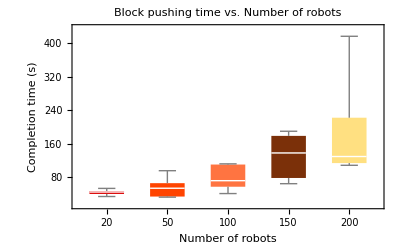

```mathematica
FontSz = 16;SetDirectory[NotebookDirectory[]];
BoxWhiskerChart[x ,ChartStyle->2,PlotTheme->"Scientific",LabelStyle->{Black,FontFamily->"Times",FontSize->FontSz},
PlotLabel-> Style["Block pushing time vs. Number of robots",FontSize->FontSz],
ChartLabels->y⟦;;,1⟧,LabelStyle->FontSz,FrameLabel->{"Number of robots",StringForm[ "Completion time (s)"]}]
Export["../pictures/pdf/AutoControlVaryN.pdf",%];
```

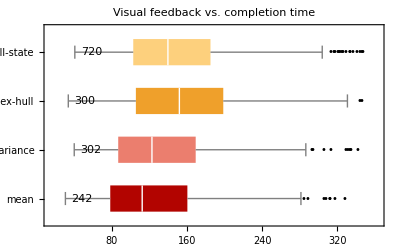

#### Circle Packing: finding the minimum variance is actually hard! http://www.math.ucsd.edu/~ronspubs/90_01_penny_packing.pdf

```mathematica
N[r^2(√3 n^2)/(4 π)]
N[Assuming[n>0&&r>0,Refine[√(r^2(√3 n^2)/(4 π))]]]
```

0.137832 n^2 r^2

0.371258 n r

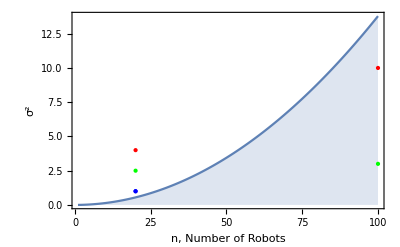

```mathematica
(*what is 'r', the radius of our robots?*)
r = .1;
DiscretePlot[{(√3 n^2 r^2)/(4 π) },{n,1,100},Joined->True,
Frame->{True,True,False,False},
LabelStyle->{Black,FontFamily->"Times",FontSize->FontSz},
FrameLabel->{"n, Number of Robots", "σ^2"},
Epilog->{PointSize->Large,
(*too small values*)Blue, Point[{{20,1},{20,1}}],
(*good values*)Green, Point[{{20,2.5},{100,3}}],
(*too big values*)Red, Point[{{20,4},{100,10}}]

}
]
```

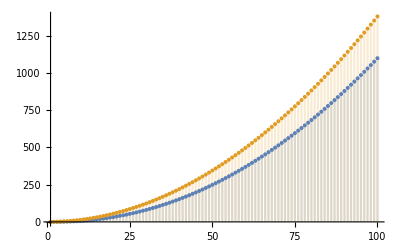

```mathematica
CircleMinVarianceLowerBound[n_]:=∑_(k=1)^n (√(3/16+(√3 (k-1))/(2 π))-(√3)/4)^2
DiscretePlot[{CircleMinVarianceLowerBound[n],(√3 n^2)/(4 π) },{n,1,100}]
```

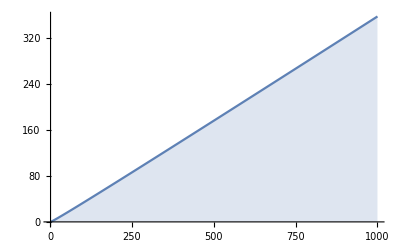

```mathematica
DiscretePlot[√CircleMinVarianceLowerBound[n],{n,1,100}]
```

```mathematica
Clear[r];Variance[UniformDistribution[{{0,(max-2r)},{0,(max-2r)}}]]
```

{1/12 (max-2 r)^2,1/12 (max-2 r)^2}

## Load data

```mathematica
SetDirectory[NotebookDirectory[]];
(*data = Import["show_results1.csv"];
data = Import["show_results0908.csv"];
data = Import["show_results0913.csv"];
data = Import["show_results0915.csv"];
data = Import["show_results1008.csv"];*)
data = Import["show_results1014.csv"];
ColNames = data⟦1⟧

(*remove bad data*)
data = Drop[data,1];
data =Select[data,#⟦1⟧!="" &]; (*some data was missing time and task name*)

TaskData=GatherBy[data,First];
FontSz = 16;
StringForm["Total experiments = ``",Length[data]]
StringForm["unique players = ``",Length[DeleteDuplicates[data,#1⟦3⟧==#2⟦3⟧&]]]
dates = Sort[data⟦;;,5⟧];
StringForm["Hours played = ``",Total[data⟦;;,4⟧]/(60*60)]
StringForm["Game Launched at = ``",dates⟦1⟧]
```

{Task,Mode,Participant,Run time,Created at,Robot count,}

Total experiments = 11936

$Aborted

Hours played = 391.071

Game Launched at = 2013-08-07 19:21:22 UTC

```mathematica
np=Select[dates,DateDifference[#,"2013-08-26 09:34:20 UTC"]<0&,1];
HNind =Position[dates,np[[1]]]⟦1,1⟧
np=Select[dates,DateDifference[#,"2013-09-09 10:22:20 UTC"]<0&,1];
RHind =Position[dates,np[[1]]]⟦1,1⟧
np=Select[dates,DateDifference[#,"2013-09-10 12:34:20 UTC"]<0&,1];
IEEEind =Position[dates,np[[1]]]⟦1,1⟧
np=Select[dates,DateDifference[#,"2013-09-17 2:24:20 UTC"]<0&,1];
IEEEemailind =Position[dates,np[[1]]]⟦1,1⟧
```

171

1916

2339

5292

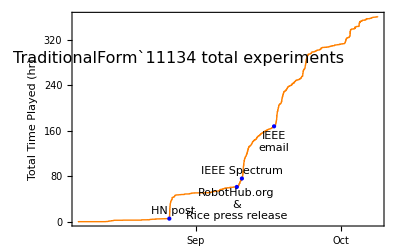

```mathematica
dateAndTime = Transpose[{dates,Accumulate[data⟦;;,4⟧]/(60*60)}];
(*Nearest[dates,{"2013-09-09 10:22:20 UTC"}]*)
bk =Directive[Opacity[0.6],White];
DateListPlot[dateAndTime,PlotStyle-> Directive[Thick,Orange],Joined->True,Frame->True,FrameLabel->{"","Total Time Played (hr)"},
LabelStyle->FontSz,
Epilog->{PointSize[Large],Blue,
Point[dateAndTime⟦HNind⟧],
Point[dateAndTime⟦RHind⟧],
Point[dateAndTime⟦IEEEind⟧],
Point[dateAndTime⟦IEEEemailind⟧],
Black,
Text["HN post",{"2013-08-27 09:34:20 UTC",20},Background->bk],
Text["RobotHub.org
&
Rice press release",{"2013-09-09 10:22:20 UTC",30},Background->bk],
Text["IEEE Spectrum",{"2013-09-10 12:34:20 UTC",90},Background->bk],
Text["IEEE
email",{"2013-09-17 2:24:20 UTC",140},Background->bk],
Text[Style[StringForm["`` total experiments",Length[data]], FontSz], {"2013-08-28 10:22:20 UTC",0.8Total[data⟦;;,4⟧]/(60*60)}]
}]
Export["../../pictures/pdf/timePlayed.pdf",%];
```

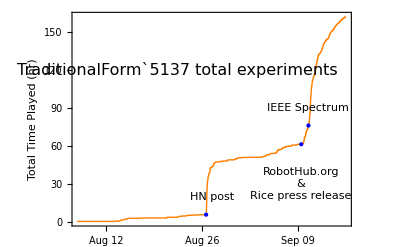

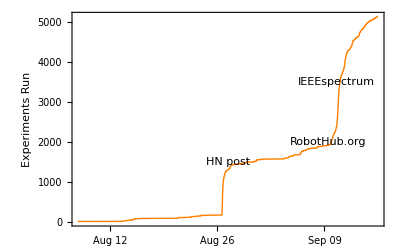

```mathematica
DateListPlot[Transpose[{dates,Table[i,{i,Length[dates]}]}],PlotStyle-> Directive[Thick,Orange],Joined->True,Frame->True,FrameLabel->{"","Experiments Run"},LabelStyle->FontSz,Epilog->{Text["HN post",{"2013-08-27 09:34:20 UTC",1500},Background->bk],Text["RobotHub.org",{"2013-09-09 10:22:20 UTC",2000},Background->bk],Text["IEEEspectrum",{"2013-09-10 12:34:20 UTC",3500},Background->bk]}]
Export["../../pictures/pdf/totalExperimentsRun.pdf",%];
```

```mathematica
PeopleData=GatherBy[data,#[[3]]&];
Length[PeopleData]
Length[TaskData]
```

1239

5

### Other plotting styles

```mathematica
TaskData=GatherBy[data,First];
```

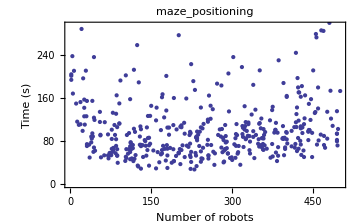
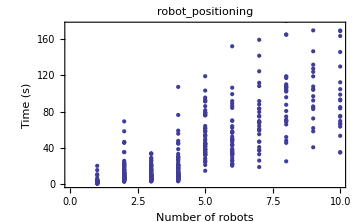

```mathematica
Table[
ListPlot[Transpose[{TaskData⟦n,;;,6⟧,TaskData⟦n,;;,4⟧}],ImageSize->Medium,Frame->{True,True,False,False},FrameLabel->{"Number of robots","Time (s)"},PlotLabel-> TaskData⟦n,1,1⟧],{n,{3,5}}]
```

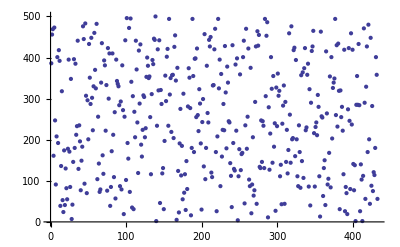

```mathematica
ListPlot[TaskData[[3,;;,6]],AxesOrigin->{0,0}]
```

## PLot for histogram Vary Noise

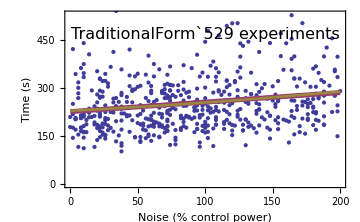

```mathematica
n=1;
dp = Transpose[{20*TaskData⟦n,;;,2⟧,TaskData⟦n,;;,4⟧}];
lpdp = ListPlot[dp,Frame->True,FrameLabel->{"Noise (% control power)","Time (s)"},LabelStyle->FontSz,
 Epilog->{Text[Style[StringForm[ "`` experiments",Length[dp]], FontSz],{100,470},Background->Directive[Opacity[0.6],White]]},ImageSize->Medium(*,PlotLabel-> TaskData⟦n,1,1⟧*)];
model=LinearModelFit[dp,x,x];
nlm=NonlinearModelFit[dp,{a x^2+b x +c},{a,b,c},x];
Show[lpdp,Plot[{model["BestFit"],nlm[x]},{x,0,200},PlotStyle-> {{Thickness[.01],ColorData[1,2]},{Thickness[.005],ColorData[1,3]}}]]
Export["../../pictures/pdf/ResVaryNoise.pdf",%];
```

## PLot for histogram Vary number of robots

```mathematica
Framed[Style[StringForm[ "``",Length[SameLength⟦n⟧]], halfFontSize],RoundingRadius->5,FrameStyle->ColorData[1,n],Background->White]
```

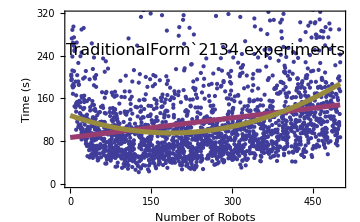

```mathematica
n=3;
dp = Transpose[{TaskData⟦n,;;,6⟧,TaskData⟦n,;;,4⟧}];
lpdp = ListPlot[dp,Frame->True,FrameLabel->{"Number of Robots","Time (s)"},LabelStyle->FontSz,ImageSize->Medium, Epilog->{Text[Style[StringForm[ "`` experiments",Length[dp]], FontSz],{250,250},Background->Directive[Opacity[0.6],White]]}(*Style[Length[dp], " results",PlotLabel-> TaskData⟦n,1,1⟧*)];
model=LinearModelFit[dp,x,x];
nlm=NonlinearModelFit[dp,{a x^2+b x +c},{a,b,c},x];
Show[lpdp,Plot[{model["BestFit"],nlm[x]},{x,0,500},PlotStyle-> {{Thickness[.01],ColorData[1,2]},{Thickness[.01],ColorData[1,3]}}]]
Export["../../pictures/pdf/ResVaryNum.pdf",%];
```

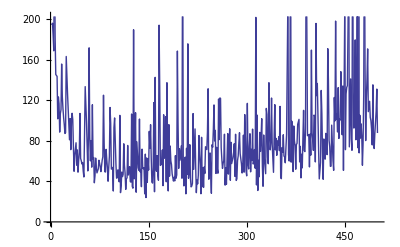

```mathematica
(* I thought it would be cool to plot the minium curve -- but our data isn't quite that dense *)
dataByNum =GatherBy[Sort[dp],First];
ListPlot[Table[{dataByNum⟦n,1,1⟧,Min[dataByNum⟦n,;;,2⟧]},{n,1,Length[dataByNum]}],Joined->True]
```

## Do players learn?

```mathematica
TaskData⟦3,1⟧
```

{maze_positioning,default,4109377799754af37569957036e9c12d,230.543,2013-08-07 19:30:02 UTC,386,}

```mathematica
PeopleVaryNum = GatherBy[TaskData⟦3⟧,#⟦3⟧&];
SameLength =Sort[GatherBy[PeopleVaryNum,Length[#]&]];
```

```mathematica
Sort[ Table[{Length[SameLength⟦n⟧], Length[SameLength⟦n,1⟧]},{n,Length[SameLength]}]]
```

{{1,8},{1,11},{1,12},{1,13},{1,18},{1,50},{2,20},{3,10},{4,7},{11,6},{19,4},{36,5},{54,3},{127,2},{541,1}}

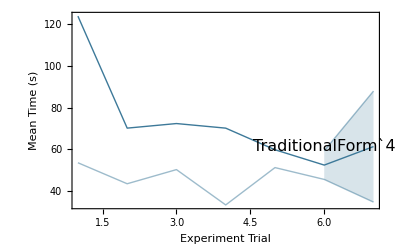
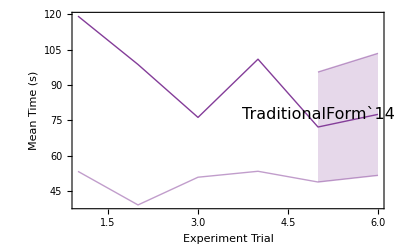
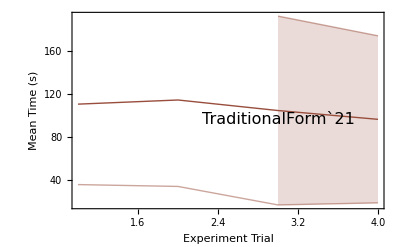
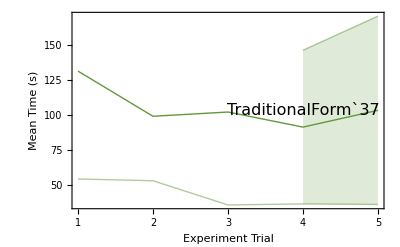
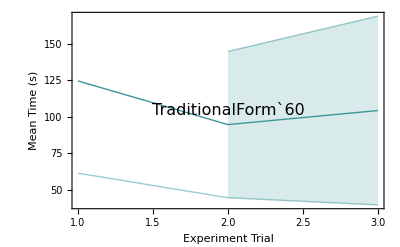
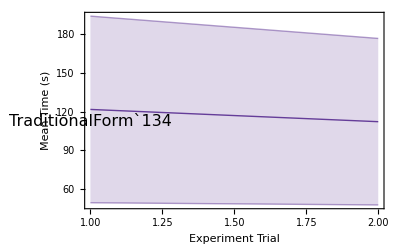
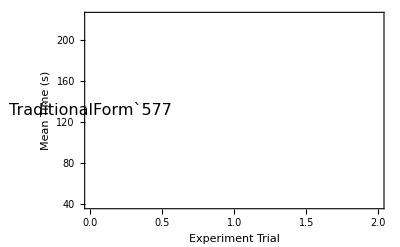

```mathematica
ploz =Table[If[Length[SameLength⟦n⟧]>3,ListPlot[ Transpose[Table[M=Mean[SameLength⟦n,;;,k,4 ⟧];S=StandardDeviation[SameLength⟦n,;;,k,4 ⟧];
{{k,M},{k,If[k≥ Length[SameLength⟦n,1⟧]-1,M+S,{}]},{k,M-S}},{k,Length[SameLength⟦n,1⟧]}]],Filling->{2->{{3},Directive[Opacity[0.2],ColorData[1,n]]}},PlotStyle->{{Directive[Thick,ColorData[1,n]]},{Directive[Thin,Opacity[0.5],ColorData[1,n]]},{Directive[Thin,Opacity[0.5],ColorData[1,n]]}},LabelStyle->FontSz,PlotRange->All,AxesOrigin->{1,0},Joined->True,Frame->True,FrameLabel->{"Experiment Trial","Mean Time  (s)"},Epilog->{Text[Style[StringForm[ "``",Length[SameLength⟦n⟧]], FontSz],{Length[SameLength⟦n,1⟧]-1,M}]}],##&[]],{n,Length[SameLength]}]
```

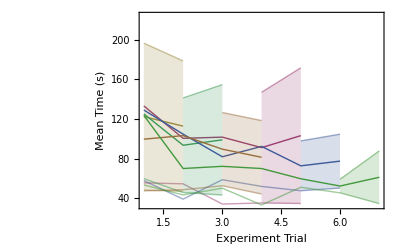

```mathematica
Show[ploz ]
```

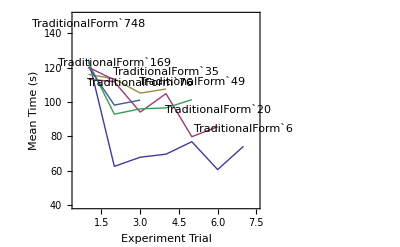

```mathematica
halfFontSize = 20;
ListPlot[ Table[If[Length[SameLength⟦n⟧]>5,Table[M=Mean[SameLength⟦n,;;,k,4 ⟧];S=StandardDeviation[SameLength⟦n,;;,k,4 ⟧];
{k,M},{k,Length[SameLength⟦n,1⟧]}],##&[]],{n,Length[SameLength]}],LabelStyle->halfFontSize,AxesOrigin->{.5,3},PlotStyle-> Directive[Thick],Joined->True,Frame->True,FrameLabel->{"Experiment Trial","Mean Time  (s)"},
PlotRange->{{0.5,7.5},{40,150}},Epilog->{Table[If[Length[SameLength⟦n⟧]>3,
k=Length[SameLength⟦n,1⟧];
M=Mean[SameLength⟦n,;;,k,4 ⟧];
Inset[Framed[Style[StringForm[ "``",Length[SameLength⟦n⟧]], halfFontSize],RoundingRadius->5,FrameStyle->ColorData[1,n],Background->White],{Length[SameLength⟦n,1⟧],M+10}],##&[]]
,{n,Length[SameLength]}]}]
Export["../../pictures/pdf/measureLearning.pdf",%];
```

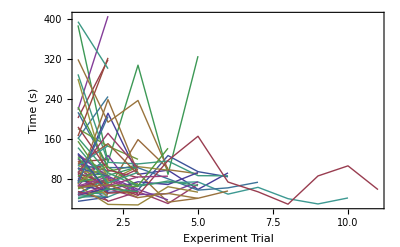

```mathematica
ListPlot[ Table[Table[{k,PeopleVaryNum⟦n,k,4 ⟧},{k,Length[PeopleVaryNum⟦n⟧]}],{n,Length[PeopleVaryNum]}],Joined->True,LabelStyle->FontSz,PlotRange->All,AxesOrigin->{1,0},Frame->True,FrameLabel->{"Experiment Trial","Time (s)"}]
```

## PLot for Robot Positioning

A box - and - whisker plot (sometimes called simply a box plot) is a histogram - like method of displaying data, invented by J.Tukey.To create a box - and - whisker plot, draw a box with ends at the quartiles Q_ 1 and Q_ 3. Draw the statistical median M as a horizontal line in the box.Now extend the "whiskers" to the farthest points that are not outliers (i.e., that are within 3/2 times the interquartile range of Q_ 1 and Q_ 3).Then, for every point more than 3/2 times the interquartile range from the end of a box, draw a dot.If two dots have the same value, draw them side by side (Gonick and Smith 1993, p.21).Box - and - whisker plots are implemented as BoxWhiskerPlot[data] in the Mathematica package StatisticalPlots`.
http://mathworld.wolfram.com/Box-and-WhiskerPlot.html

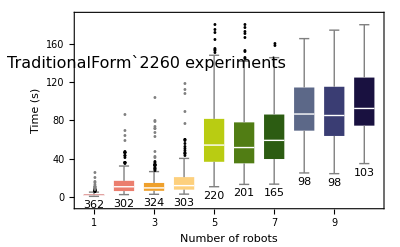

```mathematica
task = 5;
rPositioning =GatherBy[Sort[Transpose[{TaskData⟦task,;;,6⟧,TaskData⟦task,;;,4⟧}]],First];
posModes = rPositioning⟦;;,1,1⟧;
cleanPos = rPositioning⟦;;,;;,2⟧;
cleanPos = Table[DeleteCases[cleanPos⟦k,;;⟧,n_/;n>180],{k,1,Length[cleanPos]}];
BoxWhiskerChart[cleanPos,{"Outliers",{"MedianMarker",1,Directive[Thick,White]}},
ChartLabels->Placed[{posModes,Length/@cleanPos},{Axis,Below}],
ChartStyle->10,
 Epilog->{Text[Style[StringForm[ "`` experiments",Length[TaskData⟦task⟧]], FontSz],{2.75,140},
Background->Directive[Opacity[0.6],White]]},
ChartLabels->posModes,LabelStyle->FontSz,FrameLabel->{"Number of robots","Time (s)"}(*,PlotLabel-> TaskData⟦task,1,1⟧*)]
Export["../../pictures/pdf/ResPositioning.pdf",%];
```

```mathematica
Needs["ANOVA`"]
```

```mathematica
ANOVA[cleanPos]
```

ANOVA::arg1: The 1st argument has unequal columns or rows.

## PLot for Vary Visualization

```mathematica
task = 4;
varyVisual =GatherBy[Part[TaskData⟦task⟧,;;,2;;],First];
(*varyVisual =DeleteCases[varyVisualR[[;;,;;,3]],n_/;n>2000];*)
VisualModes = varyVisual⟦;;,1,1⟧;
CleanVisual = Table[DeleteCases[varyVisual⟦n,;;,3⟧,n_/;n>350],{n,1,Length[varyVisual]}];
BoxWhiskerChart[CleanVisual ,{"Outliers",{"MedianMarker",1,Directive[Thick,White]}},
ChartLabels->Placed[{VisualModes,Length/@CleanVisual},{Axis,Left}],ChartStyle->10,
PlotLabel-> Style["Visual feedback vs. completion time",FontSize->FontSz],
ChartLabels->varyVisual⟦;;,1,1⟧,BarOrigin->Left,LabelStyle->FontSz,FrameLabel->{StringForm[ "Time (s), `` experiments",Length[TaskData⟦task⟧]]}(*,PlotLabel-> TaskData⟦task,1,1⟧*)]
Export["../../pictures/pdf/ResVaryVis.pdf",%];
```

-Graphics-

### Anova Analysis (null hypothesis: the visualization type does not matter) one-way analysis of variance

```mathematica
Needs["ANOVA`"]
CleanVisual =Select[Partition[Flatten[ Table[Transpose[{varyVisual⟦n,;;,1⟧,varyVisual⟦n,;;,3⟧}],{n,1,Length[varyVisual]}]],2], #⟦2⟧<350 &];
ANOVA[CleanVisual]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 3 | 192312. | 64104.2 | 15.9555 | 3.21057×10^-10
Error | 1560 | 6.26758×10^6 | 4017.68 |  | 
Total | 1563 | 6.45989×10^6 |  |  | ,CellMeans→All | 145.988
Model[convex-hull] | 158.288
Model[full-state] | 151.732
Model[mean] | 126.676
Model[mean & variance] | 135.549}

### Using the RAW data, the results are less conclusive Anova Analysis (null hypothesis: the visualization type does not matter) one-way analysis of variance

```mathematica
Needs["ANOVA`"]
ANOVA[Transpose[{Flatten[varyVisual⟦;;,;;,1⟧],Flatten[varyVisual⟦;;,;;,3⟧]}]]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 3 | 211312. | 70437.4 | 1.06576 | 0.362509
Error | 1620 | 1.07068×10^8 | 66091.1 |  | 
Total | 1623 | 1.07279×10^8 |  |  | ,CellMeans→All | 164.37
Model[convex-hull] | 175.202
Model[full-state] | 162.436
Model[mean] | 141.918
Model[mean & variance] | 176.259}

## PLot for vary control

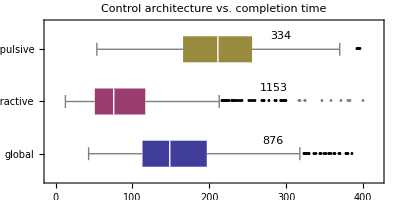

```mathematica
task = 2;
varyControl =GatherBy[Part[TaskData⟦task⟧,;;,2;;],First];
cleanControl=Table[DeleteCases[varyControl[[n,;;,3]],n_/;n>400] ,{n,1,Length[varyControl]}];
controlModes = varyControl⟦;;,1,1⟧;
BoxWhiskerChart[cleanControl,{"Outliers",{"MedianMarker",1,Directive[Thick,White]}},
ChartLabels->Placed[{controlModes,Length/@cleanControl},{Axis,{.70,1}}],
AspectRatio->.5,
PlotLabel-> Style["Control architecture vs. completion time",FontSize->FontSz],
ChartStyle->1,ChartLabels->varyControl⟦;;,1,1⟧,BarOrigin->Left,LabelStyle->FontSz,FrameLabel->{StringForm[ "Time (s), `` experiments",Length[TaskData⟦task⟧]]}]
Export["../../pictures/pdf/ResVaryControl.pdf",%];
```

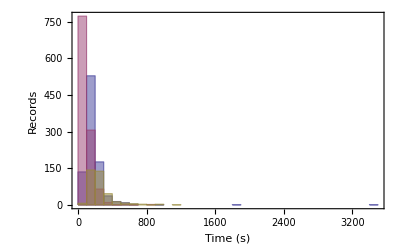

```mathematica
varyControl =GatherBy[Part[TaskData⟦2⟧,;;,2;;],First];
(*ListPlot[Table[varyControl⟦n,;;,3⟧,{n,1,3}]]*)
Histogram[Table[varyControl⟦n,;;,3⟧,{n,1,3}],30,Frame->True,LabelStyle->FontSz,FrameLabel->{"Time (s)","Records"}]
```

### Anova Analysis (null hypothesis: the control type does not matter)

```mathematica
Needs["ANOVA`"]
ANOVA[Transpose[{Flatten[varyControl⟦;;,;;,1⟧],Flatten[varyControl⟦;;,;;,3⟧]}]]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 2 | 7.93379×10^6 | 3.96689×10^6 | 278.387 | 1.39622×10^-109
Error | 2429 | 3.46122×10^7 | 14249.6 |  | 
Total | 2431 | 4.25459×10^7 |  |  | ,CellMeans→All | 149.408
Model[attractive] | 95.1847
Model[global] | 177.45
Model[repulsive] | 251.219}

### Anova Analysis Of Data from Robot Manip (null hypothesis: the control type does not matter)

```mathematica
ConstantArray["R",4]
```

{R,R,R,R}

```mathematica
Needs["ANOVA`"]
k=30;(*convert to the same time scale*)
n={1,3,5,8};
R={{2480,7050,10465,821*k},
{3319,7629,11809,687*k},
{3095,10610,22488,985*k},
{3259,6480,11116,1378*k},
{2631,34758,9155,1585*k}};
G={{2480,5879,6037,2224*k},
{3319,13524,9127,1664*k},
{3095,8127,29941,659*k},
{3259,17452,25624,954*k},
{2631,9775,24228,2152*k}};
B={{2480,1804,4032,302*k},
{3319,8393,5376,1233*k},
{3095,3376,11362,1174*k},
{3311,3188,6817,191*k},
{2631,20641,5552,190*k}};
R=R/k;
G=G/k;
B=B/k;
R⟦;;,1⟧
G⟦;;,1⟧
B⟦;;,1⟧

Table[ANOVA[Transpose[{Flatten[{ConstantArray["ADDRESSABLE"<>ToString[n⟦i⟧],5],ConstantArray["LOCAL"<>ToString[n⟦i⟧],5],ConstantArray["GLOBAL"<>ToString[n⟦i⟧],5]}],Flatten[{R⟦;;,i⟧,G⟦;;,i⟧,B⟦;;,i⟧}]}]],{i,Length[n]}]
```

{248/3,3319/30,619/6,3259/30,877/10}

{248/3,3319/30,619/6,3259/30,877/10}

{248/3,3319/30,619/6,3311/30,877/10}

{{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 2 | 0.400593 | 0.200296 | 0.00122987 | 0.998771
Error | 12 | 1954.31 | 162.859 |  | 
Total | 14 | 1954.71 |  |  | ,CellMeans→All | 98.6756
Model[ADDRESSABLE1] | 98.56
Model[GLOBAL1] | 98.9067
Model[LOCAL1] | 98.56},{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 2 | 95407. | 47703.5 | 0.565586 | 0.582461
Error | 12 | 1.01212×10^6 | 84343.5 |  | 
Total | 14 | 1.10753×10^6 |  |  | ,CellMeans→All | 352.636
Model[ADDRESSABLE3] | 443.513
Model[GLOBAL3] | 249.347
Model[LOCAL3] | 365.047},{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 2 | 424751. | 212375. | 3.79404 | 0.052861
Error | 12 | 671712. | 55976. |  | 
Total | 14 | 1.09646×10^6 |  |  | ,CellMeans→All | 429.176
Model[ADDRESSABLE5] | 433.553
Model[GLOBAL5] | 220.927
Model[LOCAL5] | 633.047},{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 2 | 2.08305×10^6 | 1.04152×10^6 | 3.37484 | 0.0687267
Error | 12 | 3.70338×10^6 | 308615. |  | 
Total | 14 | 5.78643×10^6 |  |  | ,CellMeans→All | 1079.93
Model[ADDRESSABLE8] | 1091.2
Model[GLOBAL8] | 618.
Model[LOCAL8] | 1530.6}}

## How many games per player?

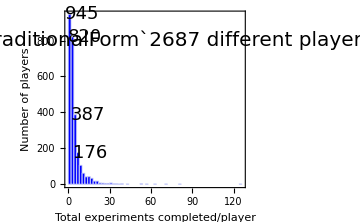

```mathematica
halfFontSize = 20;
PeopleData=GatherBy[data,#⟦3⟧&];
Histogram[Table[Length[PeopleData⟦n⟧],{n, Length[PeopleData]}],80,Frame->True,FrameLabel->{"Total experiments completed/player","Number of players"},LabelStyle->halfFontSize,ChartStyle->Blue,ImageSize->Medium,Epilog->{Text[Style[StringForm[ "`` different players",Length[PeopleData]], FontSize->halfFontSize],{80,800}]},

(*PlotRange->{{0,60},Automatic},*)
LabelingFunction->(If[# >120 ,Placed[Style[IntegerPart[#],FontSize->18],{5,1}],
If[# ==1,"",""]]&)
] 
Export["../../pictures/pdf/gamesPerPlayer.pdf",%];
(*Mathematica 9 can do ,ScalingFunctions->{"Linear","Log"} *)
```

## Browsers used

```mathematica
googleBrowserData = Import["Analytics All Web Site Data BrowserOS.csv"]
```

{{# ----------------------------------------},{# All Web Site Data},{# Browser & OS},{# 20130814-20130913},{# ----------------------------------------},{},{Browser,Visits,Pages / Visit,Avg. Visit Duration,% New Visits,Bounce Rate},{Chrome,1856,4.55,00:05:12,84.05%,33.30%},{Firefox,612,4.18,00:05:41,80.88%,37.25%},{Safari,430,2.47,00:03:33,46.98%,62.09%},{Internet Explorer,141,3.44,00:04:15,91.49%,41.13%},{Safari (in-app),77,1.32,00:00:07,98.70%,76.62%},{Android Browser,73,1.53,00:00:44,93.15%,71.23%},{Opera,19,4.58,00:04:36,94.74%,42.11%},{Opera Mini,4,1.25,00:00:01,100.00%,75.00%},{(not set),2,9.,00:03:28,100.00%,0.00%},{IE with Chrome Frame,2,1.5,00:00:19,100.00%,50.00%},{,3222,4.,00:04:47,79.52%,40.22%},{},{Day,Visits},{8/14/13,11},{8/15/13,4},{8/16/13,3},{8/17/13,0},{8/18/13,1},{8/19/13,4},{8/20/13,11},{8/21/13,17},{8/22/13,35},{8/23/13,18},{8/24/13,8},{8/25/13,9},{8/26/13,1567},{8/27/13,213},{8/28/13,50},{8/29/13,29},{8/30/13,44},{8/31/13,19},{9/1/13,9},{9/2/13,17},{9/3/13,40},{9/4/13,62},{9/5/13,57},{9/6/13,27},{9/7/13,32},{9/8/13,13},{9/9/13,30},{9/10/13,63},{9/11/13,444},{9/12/13,214},{9/13/13,171},{,3222},{}}

```mathematica
googleBrowserData⟦8;;16,2⟧
```

{1856,612,430,141,77,73,19,4,2}

```mathematica
l = 14;
pts=8;;l;
PieChart[googleBrowserData⟦pts,2⟧,ChartLabels->Placed[Table[StringForm["``%``",NumberForm[N[100*googleBrowserData⟦p,2⟧/tot],2],googleBrowserData⟦p,1⟧],{p,8,l}],"RadialCenter"],ChartStyle->"DarkRainbow"]
```

-Graphics-

```mathematica
tot = Total[googleBrowserData⟦pts,2⟧]
Table[StringForm["``%
``",NumberForm[N[100*googleBrowserData⟦p,2⟧/tot],2],googleBrowserData⟦p,1⟧],{p,8,14}]
```

3208

{"58."%
Chrome,"19."%
Firefox,"13."%
Safari,"4.4"%
Internet Explorer,"2.4"%
Safari (in-app),"2.3"%
Android Browser,"0.59"%
Opera}

## Google Analytics Demographic Data?

```mathematica
http://www.tuicool.com/articles/6JjuUb
```

```mathematica
googleData = Import["Analytics All Web Site Data Location 20130809-20130908.csv"]
```

{{# ----------------------------------------},{# All Web Site Data},{# Location},{# 20130809-20130908},{# ----------------------------------------},{},{Country / Territory,Visits,Pages / Visit,Avg. Visit Duration,% New Visits,Bounce Rate},{United States,1549,3.97,00:04:43,75.21%,42.16%},{United Kingdom,109,4.14,00:04:05,98.17%,34.86%},{Canada,103,3.12,00:03:46,96.12%,47.57%},{Germany,68,4.21,00:03:31,97.06%,29.41%},{France,41,2.9,00:02:07,95.12%,46.34%},{Brazil,38,3.66,00:03:01,92.11%,34.21%},{India,38,4.18,00:05:09,92.11%,31.58%},{Sweden,30,2.77,00:01:53,100.00%,50.00%},{Netherlands,21,5.71,00:06:11,100.00%,23.81%},{Switzerland,20,3.65,00:03:03,95.00%,45.00%},{,2314,3.82,00:04:18,81.85%,42.31%},{}}

```mathematica
<<WorldPlot`
```

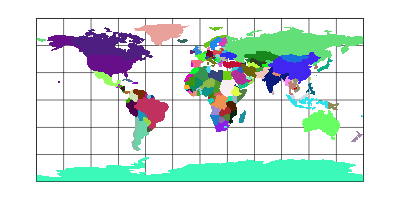

```mathematica
WorldPlot[{World,RandomColors}]
```

```mathematica
googleData[[7]]
```

{Country / Territory,Visits,Pages / Visit,Avg. Visit Duration,% New Visits,Bounce Rate}

```mathematica
googleData[[8;;]]
```

{{United States,1549,3.97,00:04:43,75.21%,42.16%},{United Kingdom,109,4.14,00:04:05,98.17%,34.86%},{Canada,103,3.12,00:03:46,96.12%,47.57%},{Germany,68,4.21,00:03:31,97.06%,29.41%},{France,41,2.9,00:02:07,95.12%,46.34%},{Brazil,38,3.66,00:03:01,92.11%,34.21%},{India,38,4.18,00:05:09,92.11%,31.58%},{Sweden,30,2.77,00:01:53,100.00%,50.00%},{Netherlands,21,5.71,00:06:11,100.00%,23.81%},{Switzerland,20,3.65,00:03:03,95.00%,45.00%},{,2314,3.82,00:04:18,81.85%,42.31%},{}}

```mathematica
shadefunc[country_]:=Switch[country,
"Canada",GrayLevel[0],
"Mexico",GrayLevel[.3],
_,GrayLevel[.6]]
```

```mathematica
googleData[[8;;Length[googleData[[;;]]]-1,1]]
googleData[[8;;Length[googleData[[;;]]]-1,2]]
```

{United States,United Kingdom,Canada,Germany,France,Brazil,India,Sweden,Netherlands,Switzerland,}

{1549,109,103,68,41,38,38,30,21,20,2314}

```mathematica
Length[googleData[[8;;]]]
```

12